# Exploring Linear Correlation in Statistics

Correlation is a measure of the strength of a linear relationship between two numerical variables.

## Why do we care about correlation?

Correlation is important in Statistics because it allows us to quantify the relationship between quantities. For example, you probably have wondered if there’s a relationship between things like the amount of calories you consume and your weight, number of fast-food restaurants in a neighborhood and obesity rates, income and mortality rates, etc. The strength of a linear relationship between quantities like these ones is measured using the linear correlation coefficient. When, we say two variables are correlated, we are saying that the variables seem to have a strong relationship between each other, but be careful, correlation does imply causation.  

The correlation coefficient 𝓇  measures the strength of a linear relationship between two paired numerical variables, and it describes the direction (positive or negative) and strength of a relationship between two variables (how well data fit a straight-line patter). 

With the help of the Wolfram language and data from the Wolfram repository, we will be able to do an overview of how to calculate and interpret the correlation coefficient .

Correlation Coefficient Properties
𝓇  only measures the strength of a linear relationship. There may be nonlinear relationships.
𝓇  is always between -1 and 1 inclusive. -1 means perfect negative linear correlation and +1 means perfect positive linear correlation
𝓇  has the same sign as the slope of the regression (best fit) line
𝓇  does not change if the independent (x) and dependent (y) variables are interchanged
𝓇  does not change if the scale on either variable is changed. You may multiply, divide, add, or subtract a value to/from all the x-values or y-values without changing the value of r.
𝓇  has a Student’s t distribution

#### Sample Correlation Coefficient Formula

We need to check our data pairs have a bivariate normal distribution

𝓇=(n∑xy-(∑x)(∑y))/(√(n∑x^2-(∑x)^2)√(n∑y^2-(∑y)^2))

### Comparing and interpreting linear strength relationships from scatter plots

```mathematica
data=BlockRandom[SeedRandom[1];
Table[RandomVariate[BinormalDistribution[i],1000],{i,{-.99,-.75,-.25,-.5,0.,.25,.5,.75,.99}}]];
```

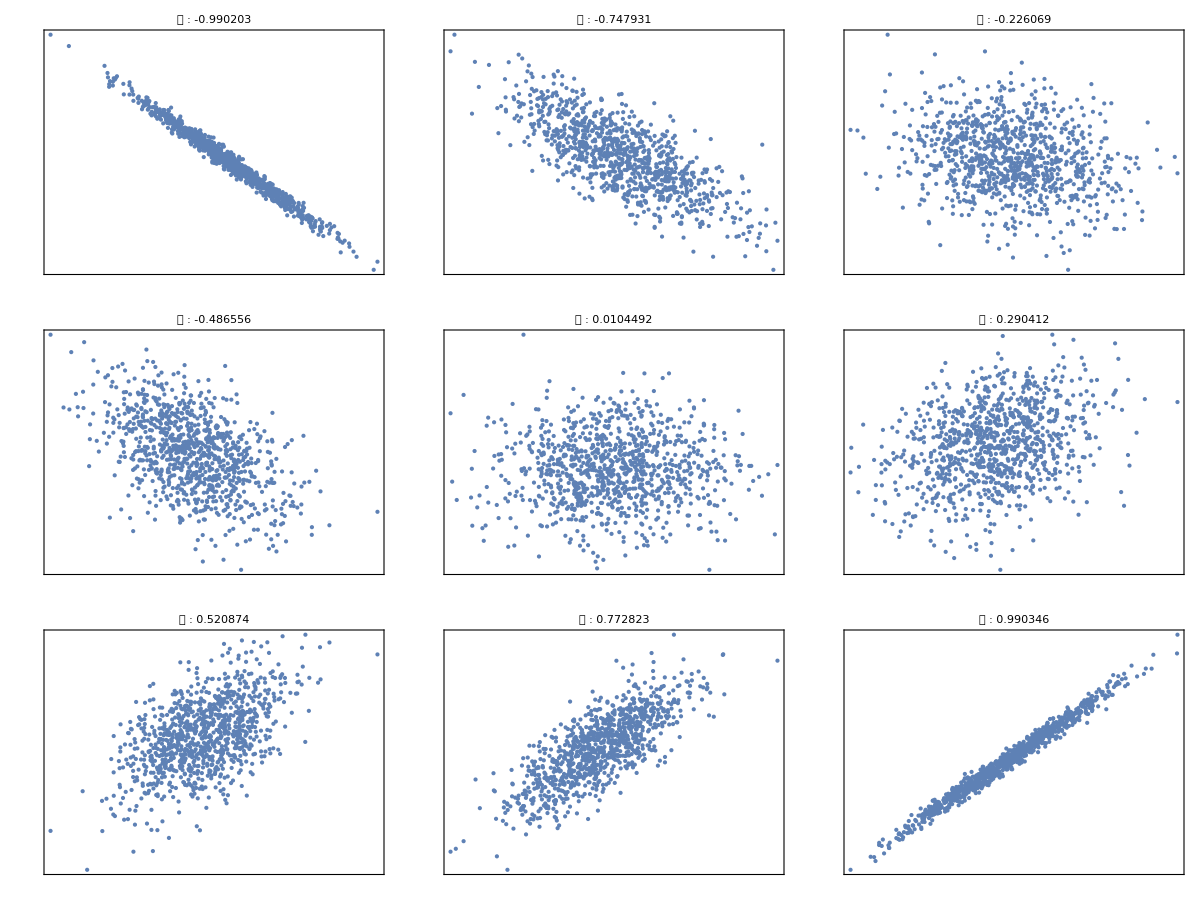

```mathematica
Grid[Partition[Table[ListPlot[i,PlotStyle->Directive[PointSize[Tiny]],FrameTicks->None,Frame->True,Axes->None,PlotLabel->Row[{"𝓇 : ",Correlation[i][[1,2]]}]],{i,data}],3]]
```

Exploring Correlation

```mathematica
Manipulate[
{x,y}=Transpose[xy];
xylim={{minx=Min[x]-f*eps,maxx=Max[x]+f*eps},{Min[y]-f*eps,Max[y]+f*eps}};
r=Correlation[Sequence@@(xy//Transpose)];
LSLine=If[LSQ,
ans=Fit[xy,{1,𝓍},𝓍];
{αLS,βLS}={First[ans],First[Last[ans]]}; {Thickness[Large],Darker[Green],Opacity[1],Line[{{minx,αLS+βLS*minx},{maxx,αLS+βLS*maxx}}]},{}];
epi={LSLine};
ListPlot[xy,
PlotStyle->{ColorData[1][1],PointSize[Large],Point[xy]},AspectRatio->1,Frame->True,Axes->False,PlotRange->xylim,FrameLabel->{X,Y},RotateLabel->False,
PlotLabel->Row[{Style["r",Italic]," = ",NumberForm[r,{6,4}]}],ImageSize->{400,400},Epilog->epi,ImagePadding->{{35,10},{35,10}}],
{{LSQ,True,Style["LS line",Darker[Green]]},{False,True},ControlPlacement->Left,ImageSize->Tiny},
{{xy,{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{29.5804,-29.5804}}},Locator,LocatorAutoCreate->{3,∞}},
{{eps,1.25},ControlType->None},
{{f,3.0},ControlType->None},
{{x,{1,2,3,4,5,6,7,8,9,29.5804}},ControlType->None},
{{y,{1,2,3,4,5,6,7,8,9,-29.5804}},ControlType->None},
AutorunSequencing->{1,2,3},
TrackedSymbols:>{xy,LSQ,L1Q,RLQ},
Initialization:>(
AndrewsData={{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{29.5804,-29.5804}};
(*L1Fit*)
L1Fit[xy_]:=Module[{𝓃=Length[xy],xy0,X,Y,rhs,c,ind,m,ans},xy0=N[xy];
{X,Y}=Transpose[xy0];
rhs=Partition[Riffle[Y,Table[0,{𝓃}]],2];
c=Join[{0.0,0.0,0.0,0.0},Table[1.0,{2 𝓃}]];ind[i_]:=Table[If[j==i,{1.0,-1.0},{0.0,0.0}],{j,𝓃}];m=Table[Flatten[{1.0,-1.0,X⟦i⟧,-X⟦i⟧,ind[i]}],{i,𝓃}];ans=LinearProgramming[c,m,rhs];Subtract[First[#],Last[#]]&/@Partition[Take[ans,4],2]];

)
]
```

### Example: Does therapy (Behavioral or Family) at an anorexia treatment center help us make any predictions on the exit weight of young female patients, given a starting weight?

```mathematica
The data below shows the before and after weight of young women undergoing anorexia treatment. When you look at the data, what kind of questions might you ask?
```

Obtain data from Wolfram Repository: Before and after weight of young women undergoing anorexia treatment.

```mathematica
datas=ResourceData["Sample Data: Anorexia Treatment"]
```

Dataset[<>]

By simply looking at data in a table, it can be difficult to observe whether or not there is a linear relationship between the entry weight and exit weight of the young female patients. A scatter diagram can help us to visualize the distribution of the data. For this example, we will examine data obtained from patients who received Behavioral Cognitive Therapy, Family Therapy, and a control group.

Select control data

```mathematica
controlData=datas[Select[#Treatment == "Cont" &]]
```

Dataset[<>]

Find the number of samples in the control group

```mathematica
Length[controlData]
```

26

Select Behavioral Cognitive Treatment data

```mathematica
btreatmentData=datas[Select[MatchQ[#Treatment ,Alternatives["CBT"]]&]]
```

Dataset[<>]

Find the number of samples in the Behavioral Cognitive Treatment group

```mathematica
Length[btreatmentData]
```

29

Select Family Therapy Data

```mathematica
ftreatmentData=datas[Select[MatchQ[#Treatment ,Alternatives["FT"]]&]]
```

Dataset[<>]

Find the number of samples in the Family Therapy Group

```mathematica
Length[ftreatmentData]
```

17

Plot Control Data

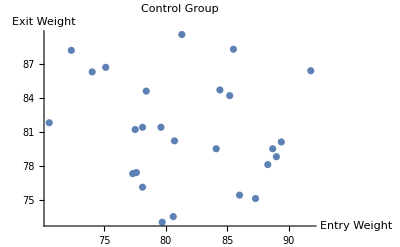

```mathematica
controlPlot1=ListPlot[controlData[All,{"EntryWeight","ExitWeight"}],PlotLabel->"Control Group",AxesLabel->{"Entry Weight","Exit Weight"}]
```

Plot Behavioral Cognitive Treatment Data

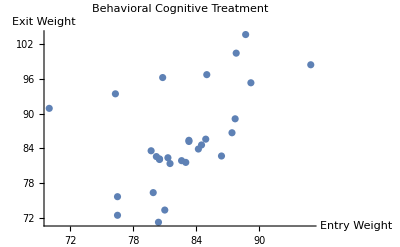

```mathematica
bTreatmentPlot=ListPlot[btreatmentData[All,{"EntryWeight","ExitWeight"}],PlotLabel->"Behavioral Cognitive Treatment",AxesLabel->{"Entry Weight","Exit Weight"}]
```

Plot Family Treatment Data

```mathematica
fTreatmentPlot=ListPlot[ftreatmentData[All,{"EntryWeight","ExitWeight"}],PlotLabel->"Family Treatment",AxesLabel->{"Entry Weight","Exit Weight"}];
```

Combine all plots to make a visual comparison

```mathematica
GraphicsGrid[{{controlPlot1,bTreatmentPlot,fTreatmentPlot}}]
```

By looking at the scatter plot, would you say there is a correlation between the entry and exit weight of the young female patients? The data is widely scattered, and by visual inspection we can observe there doesn’t seem to be a strong correlation between these two variables, but to be sure, let’s calculate the value of 𝓇 .

Compute Correlation Coefficient for Control Data

```mathematica
Correlation[Normal@controlData[All,"EntryWeight"],Normal@controlData[All,"ExitWeight"]]
```

-0.161416

Compute Correlation Coefficient for Behavioral Cognitive Therapy Data

```mathematica
Correlation[
Normal@btreatmentData[All,"EntryWeight"],
Normal@btreatmentData[All,"ExitWeight"]
]
```

0.491969

Compute Correlation Coefficient for Family Therapy Data

```mathematica
Correlation[
Normal@ftreatmentData[All,"EntryWeight"],
Normal@ftreatmentData[All,"ExitWeight"]
]
```

0.538203

## Checking for Linear Correlation

We found the values of the linear correlation coefficient for each of the three treatment scenarios in the study, but what do they mean? To interpret their meaning, we can use our knowledge on hypothesis tests and p-values. (* indicates that there is a weak linear relationship between the entry and exit weights, and we can conclude that the weights of the patients are random and there is no evidence to support that the anorexia treatments is effective.*)

(*In cases where we find a strong linear correlation, we can proceed a hypothesis test and find the line  best-fit.*)

To interpret the 𝓇  we refer to the computed p-value, if it is less that or equal to the significance level, we conclude there is a linear correlation

## Hypothesis Test using p-value from a Pearson Correlation -Test

Using the previous example, we can conduct a formal hypothesis test of the claim that there is linear correlation between the entry and exit weights.
To claim that there is linear correlation implies that the linear correlation coefficient is not zero.
H_o:ρ=0   There is no linear correlation
H_1:ρ≠ 0   There is linear correlation

(*In cases where we find a strong linear correlation, we can proceed a hypothesis test and find the line  best-fit.*)
We need to be careful how we interpret the statistical significance of a correlation. If we make a determination that our correlation coefficient is statistically significant, it does not mean that you have a strong association. It simply tests the null hypothesis that there is no relationship.

```mathematica
hypTestControl=PearsonCorrelationTest[Normal@controlData[All,"EntryWeight"],
Normal@controlData[All,"ExitWeight"],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
hypTestControl["TestDataTable"]
```

| Statistic | P-Value
Pearson Correlation | -0.161416 | 0.43083

```mathematica
hypTestControl["TestConclusion"]
```

The null hypothesis that the populations are independent is not rejected at the 5 percent level based on the Pearson Correlation test.

```mathematica
hypTestBTreatment=PearsonCorrelationTest[Normal@btreatmentData[All,"EntryWeight"],
Normal@btreatmentData[All,"ExitWeight"],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
hypTestBTreatment["TestDataTable"]
```

hypTestBTreatment[TestDataTable]

```mathematica
hypTestBTreatment["TestConclusion"]
```

The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Pearson Correlation test.

```mathematica
hypTestFTreatment=PearsonCorrelationTest[Normal@ftreatmentData[All,"EntryWeight"],
Normal@ftreatmentData[All,"ExitWeight"],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
hypTestFTreatment["TestDataTable"]
```

PearsonCorrelationTest::nortst: At least one of the p-values in {0.227102,0.00198536}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | 0.538203 | 0.0258353

## Coefficient of Variation 𝓇^2- Explained Variation

In cases where we conclude there is a linear correlation between the two variables, we can find a linear equation that expresses y in terms of x (linear regression). The value of 𝓇^2 is the proportion of the variation in y that is explained by the linear relationship between the two variables.

```mathematica
model["RSquared"]
```

0.110494

What does it mean to say there is a positively or negatively linear relationship between two variables?

## Practice Questions Using the Wolfram repository, choose a set of data and create your own notebook to do the following: 1. Load data 2. Create a scatter plot 3. based on the scatter plot, provide an estimation for the value of the correlation coefficient between the two variables and explain your answer. 4. Compute the value of the correlation coefficient

*Hypothesis Test for Correlation

Further Explorations

Multivariate Correlation
Nonlinear regression

Authorship information

Silvani Vejar

06/21/2017

e.vejar@northeastern.edu